# Physics 230 -- Lab 3 (Plotting Lists and Functions)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics & Astronomy, Fall 2011

The ability to visualize functions and data is often a prerequisite to really understanding them, especially when dealing with multi-dimensional problems.  The powerful graphical-visualization capabilities of Mathematica will enhance your ability to explore complicated functions and datasets and to present what you discover to others.

## Visualizing Data (20 minutes)

There is a lot of detail involved making plots look just the way you want them.  Most of these are things you’ll probably have to look up in the DC when you need it, unless it’s something you use all of the time.  In this introductory section, I will introduce you to basic ways of visualizing your data which you should memorize.  Later sections have information about how to Taylor these plots for special needs.

### Visualizing Functions

It is often helpful to look at a graph of a function in order to visually look for trends or other characteristics of the data.  This is done by using the Plot function with two arguments.  The first argument is an expression which can be evaluated to a real number.  The second argument defines the dependent variable and its range.  As an example, if you compute the period of a simple pendulum without making the small angle approximation you get a result in terms of a function called the complete elliptic integral of the first kind x.

```mathematica
g=9.8;
period[L_, α_]:=4 √(L/g)EllipticK[Sin[α/2]]
```

where g is acceleration due to gravity in m/s^2, α is the maximum angle the pendulum swings, and L is the length of the pendulum.  You are probably not familiar with this function and interested in seeing what it looks like as a function of angle for a 1 meter pendulum.  You can do so with the Plot command as follows.

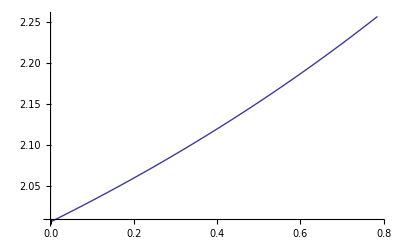

```mathematica
Plot[period[1,α], {α,0,Pi/4}]
```

For small angles, the period is

```mathematica
2*Pi*Sqrt[1/g]
```

2.00709

For larger angles, the period varies from the small angle result you derived in Physics 121.

Another time you might want to visualize a function is to find singularities which require special care in numerical work.  For example, an integral which comes up in computing the electric field generated by a 2d charge distribution involves the Bessel function 0x.  Again, this may be a function you are not familiar with, but Mathematica will easily let you visualize what it looks like.

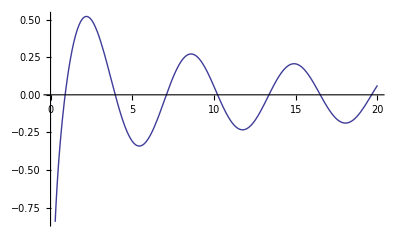

```mathematica
Plot[BesselY[0,x],{x,0,20}]
```

Apparently the function is very negative (its actually infinite) at theorigin and has a damped oscillation for larger arguments.

```mathematica
BesselY[0,0]
```

-∞

With this knowledge, you can employ special rules for numerically integrating these function which are much more accurate and stable than techniques which don’t take this behavior into account.  The functions you plot can also be functions you define yourself.  Consider the following function to compute an object’s position as a function of time while falling through the atmosphere.  Wikipedia gives the speed as

```mathematica
y[t_]:=y0-vinf^2/g Log[Cosh[g t/vinf]]
```

where y0 is the initial height, vinf is the terminal velocity, and g is acceleration due to gravity.  Using some realistic values,

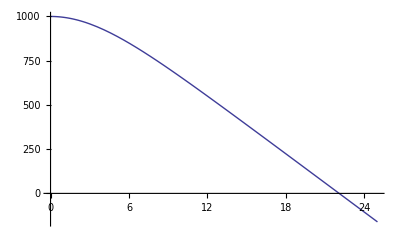

```mathematica
y0=1000;
g=9.8;
vinf=55;
Plot[y[t],{t,0,25}]
```

This graph also gives us a quick estimate of how long the object fell before fitting the ground (22 seconds) .

Some functions have a large enough range of values that they are best visualized on a plot with a logarithmic y axis.

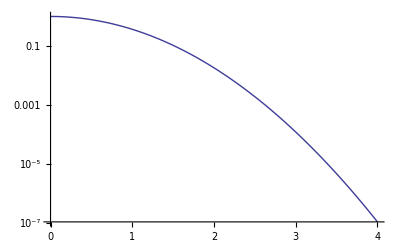

```mathematica
LogPlot[Exp[-x^2],{x,0,4}]
```

### Visualizing Data

Measured data usually comes as discrete numbers such as the data you plotted at the end of the last lab.  Such data is easily visualized using ListPlot or ListLogPlot.  As an example, the following data is the global temperature difference above the mean in hundredths of a degree C by month in the year 2001.

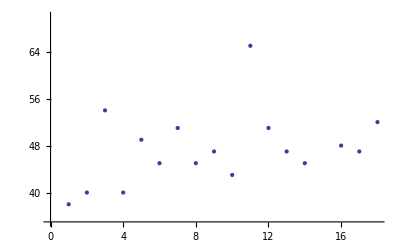

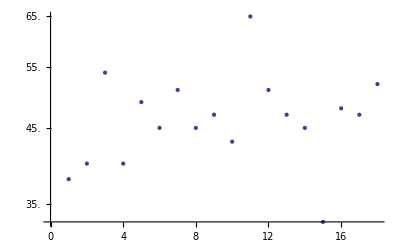

```mathematica
tempA2001={38,40,54,40,49,45,51, 45, 47, 43, 65, 51, 47, 45, 33, 48, 47, 52};
ListPlot[tempA2001,PlotRange->{35,70}]
ListLogPlot[tempA2001]
```

If the data has a large range, you can use ListLogPlot to get a logarithmic scale.  For instance, the index of refraction of boron nitride (BN) has a significant imaginary part for photon energies near 30 eV (electron Volts).   A material with a significant imaginary part of the index of refraction strongly absorbs light.  As the energy of the photons increases, the index of refraction gets very small and the material becomes more transparent.  The innermost electrons in boron have a binding energy of 188 eV.  As the photons passing through BN go through this point, these electrons are freed and suddenly increase the obsorption of light.  Likewise, nitrogen’s innermost electrons have a binding energy of 410 eV.  Going through this point provides a similar jump in the imaginary part of the index of refraction.  The plot below of the index of refraction of BN shows all of this behavior nicely.  The measured data was obtained from the CXRO web site at http://henke.lbl.gov/optical_constants/.

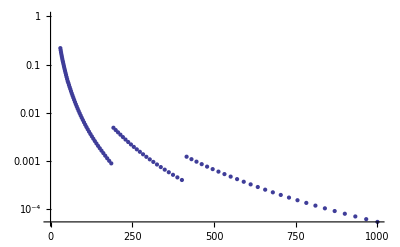

```mathematica
SetDirectory[NotebookDirectory[]];
bnIndex =Import["BN.txt","Table"];
{energy, delta, beta} = Transpose[bnIndex];
ListLogPlot[Transpose[{energy, beta}]]
```

### Three Dimensional Graphics

Sometimes acquired data or computed functions may depend on more than one parameter.  For these cases, Plot3D or ListPlot3D are useful.  For example, the spherical harmonic function (Y^m)_l(θ,ϕ)  describes the angular part of a wavefunction for an electron in an atomic p orbital.  (The wave function squared is the probability of finding the electron having that particular angular location.).  That function is plotted below as a function of θ and ϕ.

```mathematica
Plot3D[Re[SphericalHarmonicY[1,1,theta,phi]],{theta,0,Pi},{phi,0,2 Pi}]
```

-Graphics3D-

Data often comes so its best displayed on a grid as well.  Here is an example of some atomic force microscopy (AFM) data measured the height of the surface of a sample of yttrium oxide (Y2O_3).  The first row of the table has label information and the first column is the data we are interested in.  The Particition function transforms the data from a long linear list into a 256x256 matrix.

```mathematica
data=Import["afm.txt","Table"];
{data1,data2}=Transpose[Rest[data]];
dm=Partition[data1,256];
ListPlot3D[dm]
```

-Graphics3D-

Drag these figures around with your mouse and you’ll note that you can look at the data from different perspectives.

Sometimes data is more easily visualized in terms of contour plots than surfaces.  In a contour plot, points with equal values are connected by a contour line (or isoline).  You can think of these sections as the edges of the flat sections one would see if the surface plot were sliced at various surface heights. If you have ever used topographical maps when hiking or camping, those are contour plots of the height of the surface on the map.  As an example of a contour plot, the following is the same sphereical harmonic plotted in the earlier example in this section.

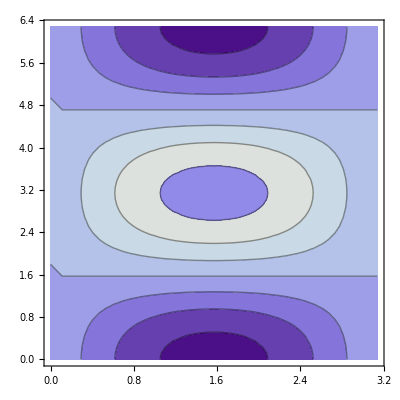

```mathematica
ContourPlot[Re[SphericalHarmonicY[1,1,theta,phi]],{theta,0,Pi},{phi,0,2 Pi}]
```

You should be able to relate what you see in this figure with the previous one.

### Graphically Finding Zeros of Legendre Polynomials (5 minutes)

Plot the 3rd, 4th, and 5th order Legendre polymials P_3(x), P_4(x) , and P_5(x)  in the range from -1 to 1 and estimate where they have a value of zero.  The Legendre polynomial P_n(x)    is represented in Mathematica as LegendreP[n,x].

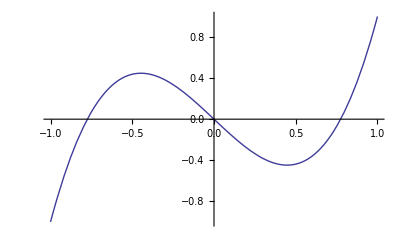

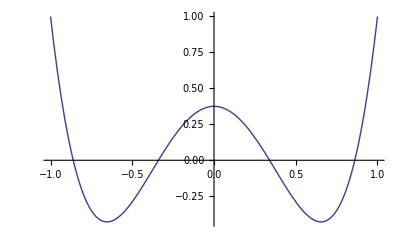

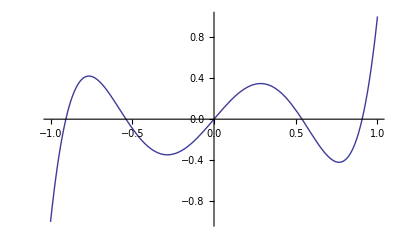

```mathematica
Plot[LegendreP[3,x],{x,-1,1}]
Plot[LegendreP[4,x],{x,-1,1}]
Plot[LegendreP[5,x],{x,-1,1}]
```

3 has zeroes at +/- 0.78 and 0.
3 has zeroes at +/- 0.86 and +/- 0.33.
5 has zeroes at +/- 0.9, +/- 0.53 and 0.

### Current and Voltage Data (5 minutes)

The following statement stores measured current and voltage data across a resistor.  Plot the data and estimate the following from the plot:
1.  Over what range is the resistor linear (i.e. where does Ohm’s Law hold)?
2.  What is the resistance of the resistor for relatively small currents?

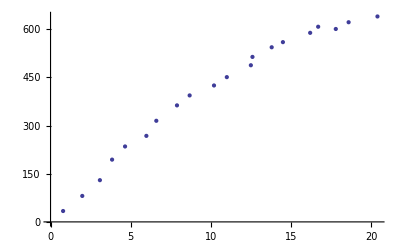

```mathematica
iv={{0.784,33.9},{1.98,80.9},{3.08,130},{3.84,194},{4.65,235},{5.98,268},{6.60,315},{7.89,363},{8.68,394},{10.2,425},{11.0,451},{12.5,488},{12.6,514},{13.8,544},{14.5,560},{16.2,589},{16.7,608},{17.8,601},{18.6,622},{20.4,640}};
ListPlot[iv]
```

### 3D Function Maximum (5 minutes)

Estimate graphically where the following function has its maximum value in the range with -2<x<2 and -3<y<2.

```mathematica
func[x_,y_]:=Module[{r},
r=Sqrt[x^2+y^2];
AiryAi[x*r]*AiryAi[y*r/Sqrt[2]]
]

Plot3D[func[x,y],{x,-2,2},{y,-3,2}](*it looks like the max is about (-.95,-1.05,0.25) *)
```

-Graphics3D-

## Plotting functions (85 min)

See the DC guide page on Function Visualization, paying special attention to Plot, ContourPlot, ParametricPlot and their 3D counterparts.  Browse the Basic Examples in the DC reference pages of each of these plot types and try to understand their input parameters.

### (#1) Plot options (15 min)

Use the special options available within the Plot function to reproduce the plot below (double-click on the thin blue group bracket if you don't see a plot).  Follow the steps below, each of which will bring you a little closer to the desired result.  And don't spend more than 15 minutes on this exercise, which can be a real time sink if you don't pace yourself.  The goal here is to get a little in-the-trench experience -- NOT to become a plotting expert.

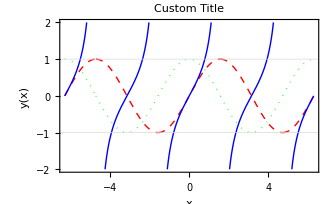

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-2Pi,2Pi},PlotRange->{-2,2},AxesOrigin->{-2Pi,0},GridLines->{None,{-1,1}},
Exclusions->{-3Pi/2,-Pi/2,Pi/2,3Pi/2},PlotStyle->{{Dashed,Thick,Red},{Dotted,Thick,Green},{Thick,Blue}},
Frame->True,FrameLabel->{"x","y(x)"},LabelStyle->Large,ImageSize->{600,400},
PlotLabel->Style["Custom Title",FontColor->Purple,FontWeight->Bold,FontFamily->"Arial",FontSize->18]]
```

(a) Browse the Options for Graphics tutorial to get warmed up.  Also open the Options section of the DC reference page for Plot to see a navigable list of options.

(b) The three curves that appear here in the range from -2π to 2π are sin(x), cos(x) and tan(x).  Evaluate the example below and observe that Plot plots each function on the same graph.

{sin(x),cos(x),tan(x)}

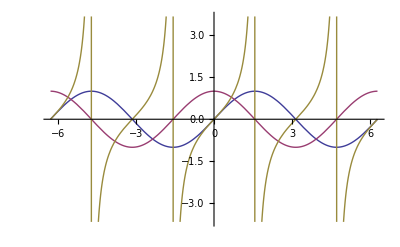

```mathematica
threefuncs = {Sin[x],Cos[x],Tan[x]}
Plot[threefuncs,{x,-2Pi,2Pi}]
```

(c) Copy the plot statement from the cell above into the cell below, and use the Frame, PlotRange, PlotStyle, PlotLabel,  FrameLabel, LabelStyle, AxesOrigin, Exclusions, GridLines, AspectRatio and ImageSize options to make your plot look as much like the pre-generated plot above as possible.  Each of these options has a default value, which may or may not be helpful depending on what you want.  Note that we don't want to see all of the things that you try along the way -- just show your best result.

PlotRange → Automatic is the default setting for PlotRange, which does a pretty good job of making sure that you see something the first time you render a graph, but rarely provides a good final product.  PlotRange → All would normally ensure that there is no y-axis clipping, but doesn't help here since tan(x) has singularities.  For this exercise, use an explicit PlotRange → {-2,2}.

PlotStyle will be useful for adjusting the color, thickness and dash-structure of the three curves.  Start with simple directives that have the same effect on all three curves.  Then try a list of three directives, so that each directive applies to a different curve.  Finally, use a list of three lists, so that each curve gets a complete list of directives.  This approach provides the freedom that you will need to reproduce the plot at the top of the exercise.  Observe that once you have customized the PlotStyle of individual curves, it is no longer possible to subsequently make PlotStyle changes that simultaneously apply to all of the curves.  Thus, to make all of the curves Thick after customizing the color of each one, we have to set the thickness of each curve separately.

PlotLabel will allow you to place the phrase "Custom Title" at the very top of the plot (as a plot title).  FrameLabel will allow you to label the horizonal and vertical plot axes as "x" and "y(x)" (keep the double quotes).  Use LabelStyle →  Large to increase the font size used throughout the plot.

{sin(x),cos(x),tan(x)}

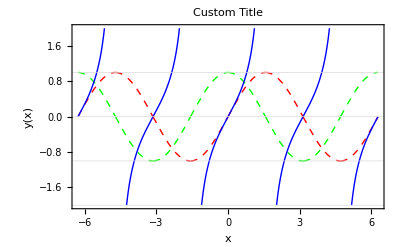

```mathematica
threefuncs = {Sin[x],Cos[x],Tan[x]}
Plot[threefuncs,{x,-2Pi,2Pi},PlotRange->{-2,2},PlotStyle->{{Red,Dashed,Thick},{Green, Dashed,Thick},{Blue,Thick}},PlotLabel->Style["Custom Title",18,FontFamily->"Arial",Purple,Bold],FrameLabel->{"x","y(x)"},Axes->False,Frame->True,LabelStyle->Large,Exclusions->Range[-2π,2π,π/2],GridLines->{None,Range[-2-2,1]}]
```

(d) In the result above, observe that LabelStyle mysteriously failed to set the font size of the plot label, even though it successfully set the size of the tick labels and the frame labels.  This smells like a bug!  But here we don't care, since we plan to set all of the style properties of the plot label separately with the Style function, which can be used to adjust the style of almost any kind of Mathematica output.  Copy your code from above and replace PlotLabel → "Custom Title" with PlotLabel → Style["Custom Title", options], and choose options like FontColor, FontWeight, FontSize and FontFamily.  We want purple, bold, 18 pt and "Arial".

### (#2) Plot editing tools (5 min)

Mathematica's integrated plot-editing tools, the Drawing Tools and Graphics Inspector items from the main Graphics menu, allow one to directly add/delete/modify a variety of components within an existing graphic.  But don't set your expectations too high -- this is definitely not PowerPoint!

Copy the graphic from the previous exercise into the space below (near the bottom of this text cell) and make the following modifications.  (a) Delete one of the function curves.  (b) Change the color, dash type, and thickness of one of the curve segments.  (c) Draw in an additional grid line.  (d) Add a label, e.g. "tan(x)", next to one of the function curves, and use the main Format: Font dialog window to change its font size, family and color (switch to the default stylesheet if you can't see it)

```mathematica
threefuncs = {Sin[x],Cos[x],Tan[x]}
Plot[threefuncs,{x,-2Pi,2Pi},PlotRange->{-2,2},PlotStyle->{{Red,Dashed,Thick},{Green, Dashed,Thick},{Blue,Thick}},PlotLabel->Style["Custom Title",18,FontFamily->"Arial",Purple,Bold],FrameLabel->{"x","y(x)"},Axes->False,Frame->True,LabelStyle->Large,Exclusions->Range[-2π,2π,π/2],GridLines->{None,Range[-2-2,1]}]
```

{sin(x),cos(x),tan(x)}

### (#3-#5) Visual problem solving (20 min)

#### (#3) Exponential and logarithmic functions (10 min)

(a) Graphically verify that  ⅇ^x ⅇ^(2 x) = ⅇ^(3 x).  This is not the same as a proof, of course.  But if you are a person who thinks visually, a graph is worth a thousand lemmas.  Hint: Plot the two functions on the same graph, and use PlotStyle to give them different colors and thicknesses (e.g. Green and Thickness[0.025] on the first curve,  Red and Thin for the second curve).

```mathematica
double = Exp[x]*Exp[2x];
single = Exp[3x];
Show[Plot[double,{x,-10,100},PlotStyle->{Green,Thick,Dashed}],Plot[single,{x,-10,100},PlotStyle->{Blue,Thin}]]
```

-Graphics-

(b) Repeat for  ln(x)+ln(3x)=ln(3 x^2).  To avoid computing the logarithm of a negative number, use a plot range that extends from 0.01 to 2.

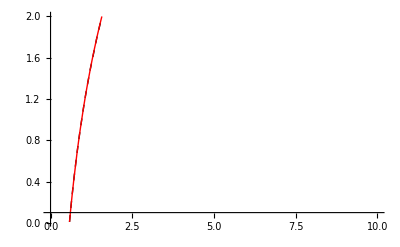

```mathematica
Show[Plot[Log[x]+Log[3x],{x,0,10},PlotRange->{0.01,2},PlotStyle->{Black,Dashed,Thick}],Plot[Log[3*x^2],{x,-10,10},PlotRange->{0.01,2},PlotStyle->{Red}]]
```

#### (#4) Log-scale plots (5 min)

Mathematica has a plethora of logarithmic plot functions (LogPlot, LogLogPlot, LogLinearPlot, etc.) depending on which axis you want to have logarithmic.

(a) In the cell below, we use each of Plot, LogPlot, LogLinearPlot and LogLogPlot to graph e^x over the range from x = 0.01 to 100.  Which log-scale scheme produced linear output and why?

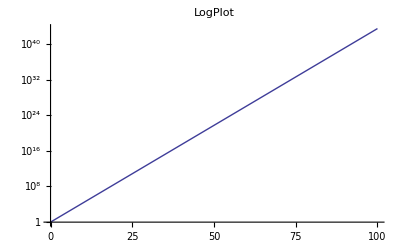
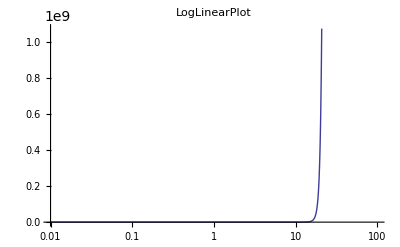
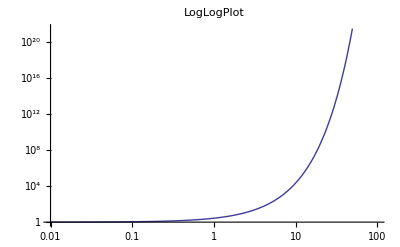
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
f[x_] :=Exp[x]
(#[f[x],{x,0.01,100},PlotLabel->#]&) /@ {Plot,LogPlot,LogLinearPlot,LogLogPlot}
```

The LogPlot produced a linear plot because we were plotitng the log where y = e^xwhich is means we are really plotting y = ln[Exp[x]] = x.

(b) Repeat for ln(x).

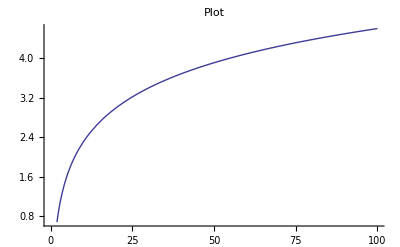
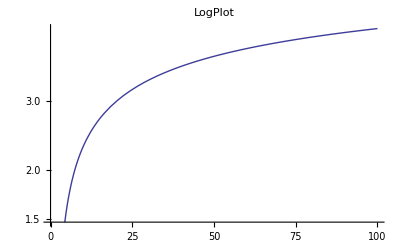
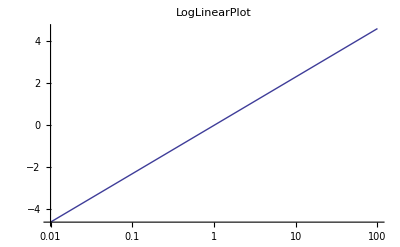
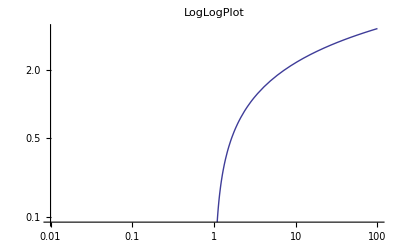

```mathematica
f[x_]:=Log[x]
(#[f[x],{x,0.01,100},PlotLabel->#]&)/@{Plot,LogPlot,LogLinearPlot,LogLogPlot}
```

Here we are plotting y = Log[x] and the LogLinearPlot is the one we want for a linear output because we are logrithmically scaling he x axis. This meanst we are really plotitng Log[y] = Log[x], so therefore y = x.

(c) Repeat for x^3.

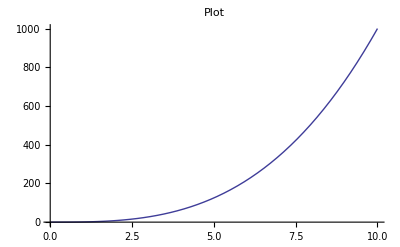
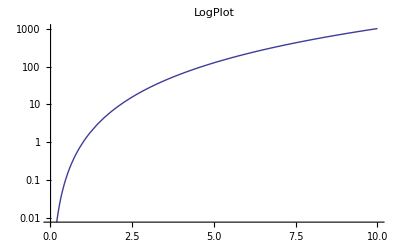
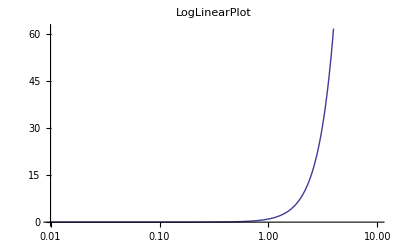
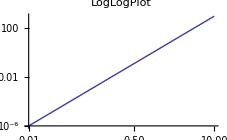

```mathematica
f[r_]:= r^3
(#[f[x],{x,0.01,10},PlotLabel->#]&)/@{Plot,LogPlot,LogLinearPlot,LogLogPlot}
```

This one needs the LogLog plot because we are effectively having a logrithmic scale on both axis and that meas we are plotting Log[y] and Log[x]. In thist case the y will be increaseing much more rapidly than the x because of y = x^3.

#### (#5) Wave superposition (5 min)

Show graphically that when you add two sin(x) and cos(x) together, you get another sinusoidal function of the form A cos(x-ϕ), where A is the new amplitude and ϕ is the new phase.  Hint: plot {A cos(x-ϕ), sin(x), cos(x), sin(x)+cos(x)} over the range from -2π to 2π, giving each curve a different color, and making A cos(x-ϕ) lighter and thicker than the others.  You will, of course, need to substitute real numbers in for A and ϕ -- determine their correct values by manually adjusting them until sin(x)+cos(x) and A cos(x-ϕ) coincide.

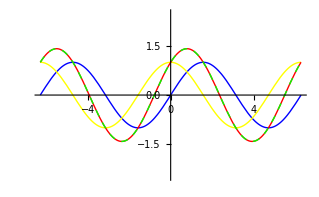

```mathematica
Show[Plot[Sin[x],{x,-2π,2π},PlotStyle->Blue,PlotRange->{-2.5,2.5}],Plot[Cos[x],{x,-2π,2π},PlotStyle->Yellow,PlotRange->{-2.5,2.5}],Plot[Sin[x]+Cos[x],{x,-2π,2π},PlotStyle-> Red,PlotRange->{-2.5,2.5}],Plot[√2 Cos[x-π/4],{x,-2π,2π},PlotStyle->{Green,Thick,Dashed},PlotRange->{-2.5,2.5}]]
```

### (#6) Plot3D (10 min)

Use  Plot3D to graph (x^2+y^2+0.1)^-1 over a sufficiently wide range of x and y to properly illustrate the central peak.  Apply PlotRange to prevent the top of the peak from getting clipped off.  Hide the Mesh and employ a simple ColorFunction to enhance the appearance.  Use BoxRatios (analogous to AspectRatio in 2D graphics) to set make the bounding box be cubic (i.e. BoxRatios → {1,1,1}).  Use Boxed (analogous to Frame in 2D graphics) to hide the bounding box, and also hide the Axes.  Apply FaceGrids → All to further customize the plot.

```mathematica
Plot3D[(x^2+y^2+.01)^-1,{x,-.35,.35},{y,-.35,.35},PlotRange->{-120,120},Mesh->None,ColorFunction->"Rainbow",BoxRatios->{1,1,1},Axes->False,FaceGrids->All,Boxed->False]
```

-Graphics3D-

### (#7) Contour plots (10 min)

The ContourPlot is a flexible tool capable of handling more than one type of visualization problem.

(a) Use both ContourPlot and Plot3D to visualize the two-variable expression cos(π x) + cos(π y) over a range that extends from -2 to 2 along both axes.  Compare and contrast the two methods of "seeing" the function.

-Graphics3D-

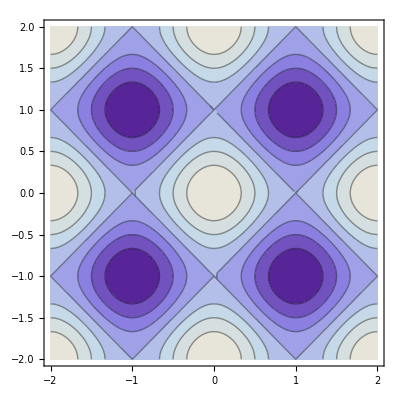

```mathematica
Plot3D[Cos[π x]+Cos[π y],{x,-2,2},{y,-2,2} ]
ContourPlot[Cos[π x]+Cos[π y],{x,-2,2},{y,-2,2} ]
```

(b) See the DC reference page for DensityPlot, which is really a specific type of contour plot with a large number of undrawn contour lines.  Evaluate the following example to demonstrate this.

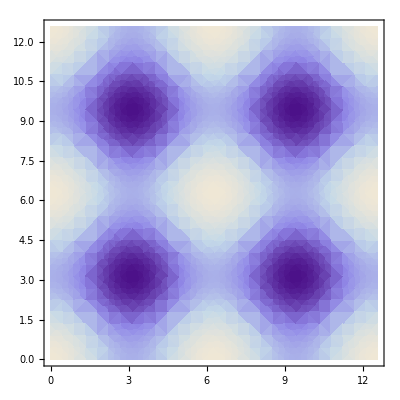

-Graphics-

```mathematica
DensityPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}]
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi},Contours->50,ContourLines->False]
```

### (#8) Contour plots of implicit equations (10 min)

Instead of feeding ContourPlot an expression, we can feed it an implicit equation,  which effectively selects the specific contour that constitutes the solution to the equation.  Thus, we have a method of visually solving implicit equations.  

(a) Define the expression func1 = Cos[π x] + Cos[π y] and use this approach to plot the contour line that satisfies the equation func1 == 1/2.  Let your plot span the range from -2 to 2 over both axes.

cos(π x)+cos(π y)

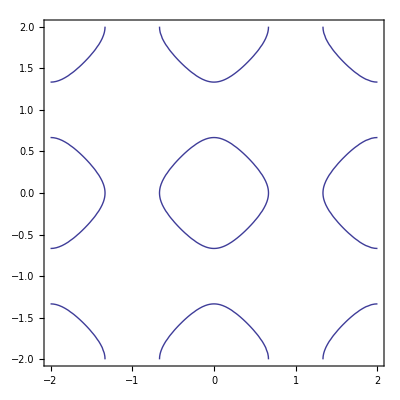

```mathematica
func1 = Cos[π x] + Cos[π y]
ContourPlot [func1==1/2,{x,-2,2},{y,-2,2}]
```

(b) In fact, if we provide a list of equations to ContourPlot, the intersection of the contours from each of the equations (if they intersect) reveal the solution to the entire system of implicit equations (i.e. the set of points that simultaneously satisfy all of the equations).  Define a second expression, func2 = x^2+y^2, and visualize the solution to the system of equations: {func1 == 1/2, func2 == 2}.  Use ContourStyle to make the two contours appear with different colors.

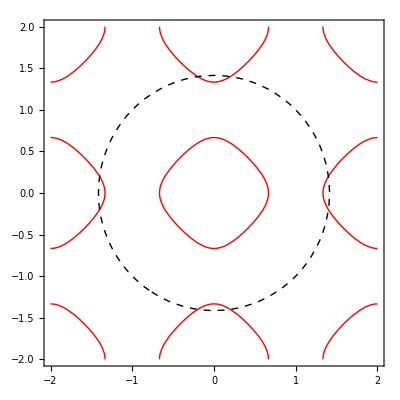

```mathematica
func1 = Cos[π x] + Cos[π y];
func2 = x^2+y^2;
ContourPlot[{func1==1/2,func2==2},{x,-2,2},{y,-2,2},ContourStyle->{Red,Dashed}]
```

You can also plot implicit equation solutions in 3D with ContourPlot3D.  See the DC reference page for examples if you have time.

### (#9) Parametric functions and plots (10 min)

A curved line in the 2D plane has one degree of freedom, i.e. your position along the line.  Let's call that variable "u".  Because we can describe any point in the 2D plane in terms of it's xy coordinates, the 1D collection of points that comprise the curve can be described by allowing both x and y to depend on u.  As we vary u, the pair of functions {x(u), y(u)} trace out a parametric curve.  This is a very general concept.  Think about it until you understand.

Consider a straight line.  Suppose that we define x(u) = u and y(u) = 3u+1.  This is the parametric equivalent of simply defining y(x) = 3x+1.  The parametric equations appear unnecessarily complicated compared to the simple y(x) form.  But the parametric approach also allows one to define and plot functions that cannot be described by a simple y(x).

(a) Evaluate the cell below, where we use both a simple function and a parametric function to describe and plot a semicircle.  Try to understand the output.

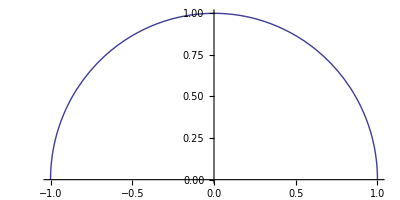

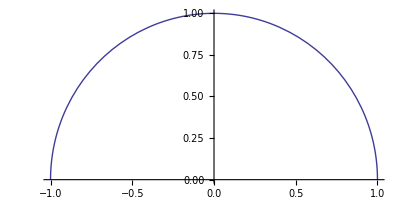

```mathematica
y[x_] := Sqrt[1-x^2]
Plot[y[x],{x,-1,1},AspectRatio->1/2]
ParametricPlot[{Cos[phi],Sin[phi]},{phi,0,Pi}]
```

(b) Evaluate the example below, where we clearly see that a parametric function is more general than a function of the form y(x).

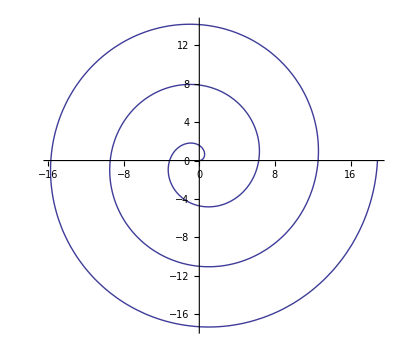

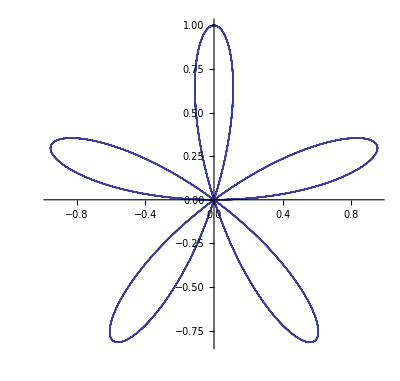

```mathematica
ParametricPlot[phi*{Cos[phi],Sin[phi]},{phi,0,6Pi}]
ParametricPlot[Cos[5*phi-Pi/2]*{Cos[phi],Sin[phi]},{phi,0,6Pi}]
```

(c) Mathematica plot functions like PolarPlot, RevolutionPlot3D and SphericalPlot3D are variations on the parametric-plot theme.  They simplify the process of constructing a parametric plot in certain specific cases.  For example, a polar plot is useful when the parametric variable is the phase angle (i.e. tan(ϕ) = y/x) and where the distance √(x^2+y^2)has an explicit dependence on ϕ.  Evaluate the example below and compare and contrast the two methods of plotting a spiral.

```mathematica
ParametricPlot[phi*{Cos[phi],Sin[phi]},{phi,0,6Pi}]
PolarPlot[phi,{phi,0,6Pi}]
```

-Graphics-

-Graphics-

(d) Now make up your own ParametricPlot example.

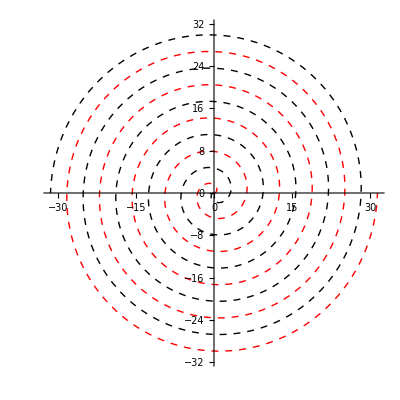

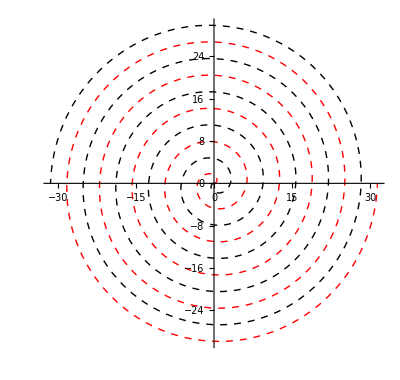

```mathematica
Show[ParametricPlot[phi*{Cos[phi],Sin[phi]},{phi,0,10π},PlotRange->{-10π,10π},PlotStyle->{Red,Dashed,Thick}],ParametricPlot[-phi*{Cos[phi],Sin[phi]},{phi,0,10π},PlotRange->{-10π,10π},PlotStyle->{Black,Dashed,Thick}]]
Show[PolarPlot[phi,{phi,0,10π},PlotStyle->{Red,Dashed,Thick}],PolarPlot[-phi,{phi,0,10π},PlotStyle->{Black,Dashed,Thick}]]
```

### (#10) Plotting parametric surfaces (5 min)

(a) Let's start by generating a few surfaces that can be parameterized by two variables: u and v.  A surface in three-dimensional space is inherently two-dimensional; hence the need for two variables.  A parametric surface is actually a list of three functions: {x(u,v), y(u,v), z(u,v)}, such that every pair of values for u and v create a point {x, y, z} on the surface.  The simplest important example is a tilted plane, where x = u and y = v, and where the height z is a linear combination of u and v.  Evaluate the cells below, and observe that the two sets of mesh lines indicate lines of constant u and constant v, respectively.

```mathematica
coolsurface[u_,v_] := {u,v,2u+v^5}
ParametricPlot3D[coolsurface[u,v],{u,-2,2},{v,-2,2}]
```

-Graphics3D-

Now, in the cell above, modify one or more of the three coordinate functions in coolsurface and see how the surface changes.  You should try simple sums, polynomials, and trigonometric and exponential functions of u and v.

(b) Can you figure out how to generate a parametric sphere?  If you have worked with spherical coordinates, this will be an easy task.  But on the off chance that you don't remember much about them, we'll show you how it's done.  We'll parameterize the sphere with two variables: ϕ and θ, where ϕ is the azimuthal angle (i.e. longitude, which varies from 0 to 2π on a trip around the equator) and θ is the zenith angle (i.e. lattitude, which varies from 0 to π on a trip from north to south pole).  In the cell below, we essentially replaced coolsurface[u,v] with sphere[ϕ,θ].  Try it and observe that the two sets of mesh lines indicate lines of constant ϕ and constant θ respectively.

```mathematica
sphere[phi_,theta_] := {Cos[phi](Sin[theta]), Sin[phi](Sin[theta]), Cos[theta]}
ParametricPlot3D[sphere[phi,theta],{phi,0,2 Pi},{theta,0,Pi}]
```

-Graphics3D-

(c) To distort the sphere into an ellipsoid, we can multiply the x, y and z-coordinate functions by different values.  Try changing the values of a, b and c, and observe the effect on the ellipsoid shape.

```mathematica
a = 10; b = 3; c =5;
ellipsoid[phi_,theta_] := {Cos[phi](a Sin[theta]),  Sin[phi](b Sin[theta]), c*Cos[theta]}
ParametricPlot3D[ellipsoid[phi,theta],{phi,0,2 Pi},{theta,0,Pi}]
```

-Graphics3D-

## Plotting data (20 min)

Scan through the DC guide page on Data Visualization, and follow the links to examples of the following functions: ListPlot, ListPlot3D, ListContourPlot and ListContourPlot3D.

### (#11) Plot options for data visualization (10 min)

Most of the plot options for ListPlot are the same as those available to Plot.  A few important additions in ListPlot include Joined, InterpolationOrder, MaxPlotPoints and  PlotMarkers.  Go to the options section of the DC references page for ListPlot and review the examples associated with each of these options.

(a) Evaluate the cell below to create a list of xy data pairs, and ListPlot the data.  Then add the Joined → True option to see its effect.

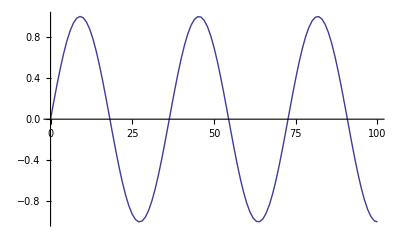

```mathematica
data = Table[{n, Sin[0.173*n]}, {n, 0, 100}];
ListPlot[data,Joined->True]
```

(b) Copy your code from above and add the MaxPlotPoints option to restrict the plot so as to include only 1/2 of the original data points.  The resulting curve should be somewhat segmented rather than smooth.  This option can be useful when you have way too many data points.

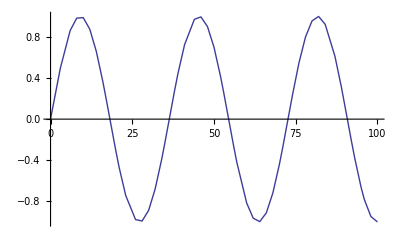

```mathematica
ListPlot[data,Joined->True,MaxPlotPoints->50]
```

(c) Copy your code from above and use InterpolationOrder to smooth the rough corners of the plot.  Try different orders of interpolation (e.g. 0, 1, 2, 3) and describe the result to your TA.

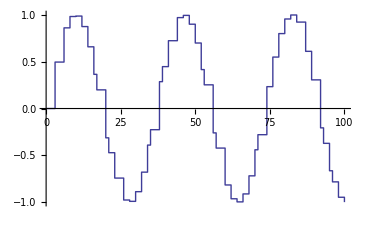
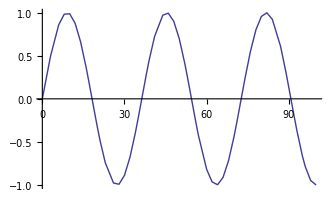
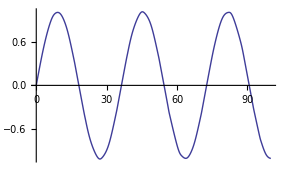

```mathematica
Table[{ListPlot[data,Joined->True,MaxPlotPoints->50,InterpolationOrder->.51],ListPlot[data,Joined->True,MaxPlotPoints->50,InterpolationOrder->1],ListPlot[data,Joined->True,MaxPlotPoints->50,InterpolationOrder->3]}]
```

### (#12) Plotting 2D data sets (10 min)

Evaluate the cell below to define a set of xyz data obtained from a radially-symmetric 2D zeroth-order Bessel function of the squared distance from the origin.  Make sure that you understand how we generated a flat list of xyz triplets.  Once you have had a good look at the data, you may want to suppress the output with a semicolon.  Use both ListPlot3D, ListContourPlot and ListPointPlot3D to visualize the data.  Try a few interesting plot options.

-Graphics3D-

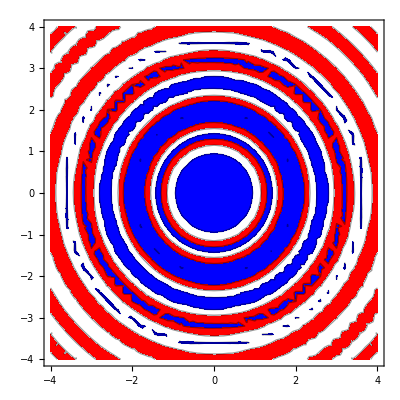

-Graphics3D-

```mathematica
data = Table[{x,y,BesselJ[0,x^2+y^2]},{x,-4,4,0.2},{y,-4,4,0.2}]//Flatten[#,1]&;
ListPlot3D[data,InterpolationOrder->.5]
ListContourPlot[data,ContourShading->{Red,White,Blue}]
ListPointPlot3D[data,ColorFunction->"Rainbow"]
```

## Advanced 3D plot options (optional, 20 min)

Using the mouse to grab a corner, expand the graphic below to fill much of the screen and take a closer look.  The objective of this exercise is to figure out how to create this plot yourself.  The problem is broken up into several steps, each one of which will bring you little closer to the final product.

```mathematica
ss = 1/2; tt=ss/2;
mytire[phi_,theta_] := {Cos[phi](1+ss Sin[theta] + tt Cos[theta]^2), Sin[phi](1+ss Sin[theta]+ tt Cos[theta]^2),  Cos[theta]*ss}
mytireplot := ParametricPlot3D[mytire[phi,theta],{phi,0,2 Pi},{theta,0,2 Pi},Evaluate[mypoptions]]

mylightsources = 10*{{0,0,-1},{0,0,1},{0,-1,0},{0,1,0},{-1,0,0},{1,0,0}};
myshine[color_] := Directive[color,Specularity[White,50],Lighting->({"Point",White,#}&/@mylightsources)]

pp =6; nn =2;  (* use n values between 0 and 2*p-1 *)
mm=4*pp; rat = (mm/(mm-2nn) - 1); 
mypoptions = {Boxed->False,Axes->False,Mesh->{mm-1,mm-1}, MeshShading->{{myshine[Blue],None},{myshine[Red],myshine[Blue]}},
MeshFunctions->{#4&,#5+rat*#4&},PlotPoints->50};

mytireplot
```

-Graphics3D-

(a) Now we want to add some plot options that modify the appearance of your tire.  Review the DC reference pages for Boxed, Axes, Mesh, PlotPoints, and modify each option (one at a time) in the cell below to get a feel for what they do.

```mathematica
tire[phi_,theta_] := {Cos[phi](1+0.5 Sin[theta] + 0.25 Cos[theta]^2), Sin[phi](1+0.5 Sin[theta]+ 0.25 Cos[theta]^2),  0.5*Cos[theta]}
ParametricPlot3D[tire[phi,theta],{phi,0,2 Pi},{theta,0,2 Pi},Boxed->False,Axes->False,Mesh->{7,20},PlotPoints->7]
```

-Graphics3D-

(b) Here, we define tireplot based on a list of plot options that hasn't been defined yet.  We subsequently place all of our plot options into a separate list called plotoptions.  When we call tireplot, which is defined using a delayed assignment, it grabs the latest version of the options just before rendering the plot.  Evaluate the cells below and explain the results to your TA.

```mathematica
tireplot := ParametricPlot3D[tire[phi,theta],{phi,0,2 Pi},{theta,0,2 Pi},Evaluate[plotoptions]];
```

```mathematica
plotoptions = {Boxed->False,Axes->False,Mesh->{23,23},PlotPoints->50};  (* use these values throughout the rest of the exercise *)
tireplot
```

-Graphics3D-

The Evaluate operation forces the evaluation of plotoptions, which would otherwise be prevented by HoldAll, an annoying attribute of many plot-related functions.  Don't worry about this right now.  We'll say more about function Attributes in a later lab.

(c) Copy/paste the previous input into the cell below and add MeshFunctions to your list of plot options, e.g. MeshFunctions → {#1&}.  Try distributing your mesh lines along each of the five principle directions (x, y, z, ϕ, θ).  Try using multiple mesh functions (i.e. a list of nameless functions), and verify that MeshFunctions → {#4 &, #5 &} is the default setting (i.e. what you get if you don't specify a mesh function).  Discuss your results with your TA.

```mathematica
plotoptions = {Boxed->False,Axes->False,Mesh->{23,23},PlotPoints->50,MeshFunctions->{#1&,#2&,#3&}};  (*I don't get this one *)
tireplot
```

-Graphics3D-

(d) Add MeshStyle and MeshShading to your list of plot options and explore their behavior.  Be warned that the Dimensions of your list of MeshShading directives must be equal to the number of MeshFunctions that you apply.  Because that was a pretty strange statement, we provide a couple of examples.
	MeshFunctions → {#1&},  MeshShading → {Red, Blue}
	MeshFunctions → {#1&, #2&},  MeshShading → {{Red, Blue}, {Pink, None}}
	MeshFunctions → {#1&, #2&, #3&},  MeshShading → {{{Red, Blue},{Blue,Red}}, {{Orange,Black},{Black,Orange}}}

(e) Remove the MeshShading and MeshStyle options for now, and add some swirl with a two-dimensional mesh of the form: MeshFunctions → {#4 &, #5 + rat *#4 &}, where rat is a number of your choice between 0 and 1.  The swirl arise because we no longer have constant θ lines, which have been replaced by constant (θ + rat *ϕ) lines.  Try a few different values of rat, finishing with rat = 0.2.

(f) Next, add some fancy lighting and surface-rendering options, which can be tricky to use!  Specularity makes surfaces reflect light.   Opacity makes surfaces partially transparent.  Lighting manipulates the types and locations of the light sources that illuminate an object.  Specularity and Opacity are best applied as directives inside a PlotStyle option as shown in these examples:
	PlotStyle → Specularity[White, 20]
	PlotStyle → Opacity[0.85]
Be warned that Opacity will significantly tax your computer's processing power unless you have a really fast graphics card.  Lighting comes in enough varieties to make your head ache.  Here are a few examples:
	Lighting → "Neutral"
	Lighting → {{"Ambient", White}}
	Lighting → {{"Point", White, {0, 0, 1}}}
Explore one option at a time in the cell below.

(g) With enough effort, we can get very nice-looking surfaces.  Here, we first define a function that renders a specific color as a shiny surface that reflects light from 6 different light sources surrounding the object, and then apply it as a PlotStyle directive.  Try it out.

```mathematica
lightsources ={"Point",White,#}&/@ {{0,0,-10},{0,0,10},{0,-10,0},{0,10,0},{-10,0,0},{10,0,0}};
shine[color_] := {color,Specularity[White,100],Lighting->lightsources}

plotoptions = {Boxed->False,Axes->False,Mesh->{23,23},MeshFunctions->{#4&,#5+0.2*#4&},PlotPoints->50,PlotStyle->shine[Orange]};
tireplot
```

(h) We can even apply the shiny surfaces to individual elements of a multi-dimensional MeshShading, as shown below.  Try it.

```mathematica
plotoptions = {Boxed->False,Axes->False,Mesh->{23,23},MeshShading->{{shine[Blue],None},{shine[Red],shine[Blue]}},MeshFunctions->{#4&,#5+0.2*#4&},PlotPoints->50};
tireplot
```

## On Your Own (45 min)

### (#13) Quantum Mechanical Square Well (15 min)

If a quantum mechanical particle is in a rectangular potential well, it has a limited number of discrete energies which depend on the height and width of the well.  We could (but won’t) show that one set of these energies can be found by solving the equations Sqrt[u0^2-v^2]==v Tan[v]  for the symmetric solutions or Sqrt[u0^2-v^2]==-v Cot[v].  Solve this equation graphically by finding the places y=Sqrt[u0^2-v^2] intersects the curve y=v Tan[v] or y=-v Cot[v].  Physically, v must be greater than 0.  Let u0=5.  How many roots did you find and what are the estimated values of v?

HINTS:  You can eliminate the asymptote lines by using the Exclusions option and excluding the points where v=Pi/2, Pi, and 3Pi/2.  The plot will be easier to read if you limit the y range to be between 0 and 5.

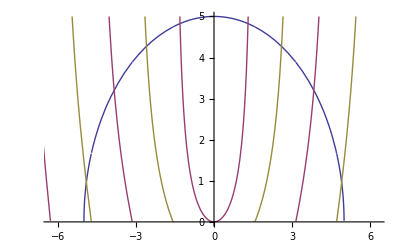

```mathematica
Plot[{√(5^2-x^2),x*Tan[x],-x*Cot[x]},{x,-2π,2π},Exclusions->Range[-15π/2,15π/2,π/2],PlotRange->{0,5}]
```

I found 8 roots and the approximate values are {-4.8,-3.8,-2.5,-1,1,2.5,3.8,4.8}

### (#14) Circular Drum Head (15 min)

A circular drum head vibrates with an amplitude y(r, θ, t)=AJ_m(kr)cos(mθ)cos(ωt) where A is the maximum amplitude of the wave, ω is the angular frequency of the vibration, m is a non-negtive integer, and k is related to the speed of sound c on the drum head according to the relation ω=kc.  J_m(x) is the Bessel function of the first kind which is the funciton BesselJ[m,x)] in Mathematica.

The drum head is clamped along the radius a which means that J_m(ka)  must be zero.  Graphically find the lowest three angular frequencies of a circular drum head with a radius a of 0.25 meters and a speed of sound c of 100 meters per second.

Generate height of the surfaces of these drum heads using A=0.1, t=0 and plot their shapes using ParametricPlot3D.

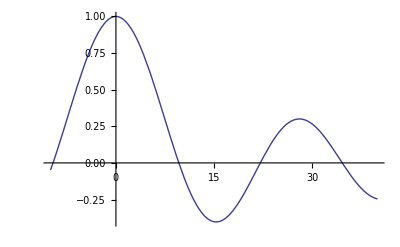

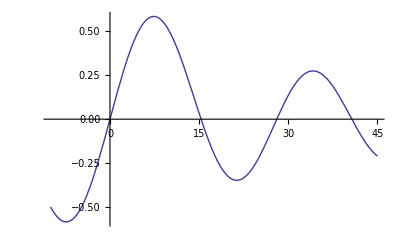

```mathematica
Plot[BesselJ[0,.25*k],{k,-10,40}]
Plot[BesselJ[1,0.25k],{k,-10,45}]
```

Assuming a Bessel functino of the 0th order k is about 9.8,22.2,34.2, so w =kc= 980,2220,3420.
Assuming a Bessel function of the first order k is about 15.2, 28.1, 40.4 so w = 1520, 2810, 4040

```mathematica
y[θ_,k_,ω_,m_]:=0.1*BesselJ[m,0.25k]*Cos[m*θ]*Cos[ω*0]
```

### (#15) Sputtering Target Motion (15 min)

When we sputter thin films, our target is on an arm that rotates around the center of our vacuum chamber at a speed ω_1=2 π.  The middle of the circular target is a distance a=3.375  from the center of the chamber.  Through some planetary gears, the target also spins about its own axis with a speed ω_2=20/3ω_1.  Using some matrix algebra which we will do in a later unit, you can show that if a point on the sample starts at the point {x2, y2}, its position {xp,yp} at time t will be xp=a Cos[ω1 t]+x2 Cos[(ω1+ω2)t]-y2 Sin[(ω1+ω2)t] and yp=a Sin[ω1 t]+x2 Sin[(ω1+ω2)t]+y2Cos[(ω1+ω2)t].  Using ParametricPlot, plot the position of the following points for three full perionds (t from 0 to 3):  {x2,y2}={0,0}, {x2,y2}={0.25,0.75}, {x2,y2}={-1, 2}.

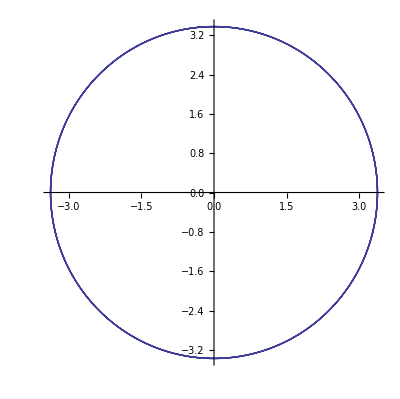

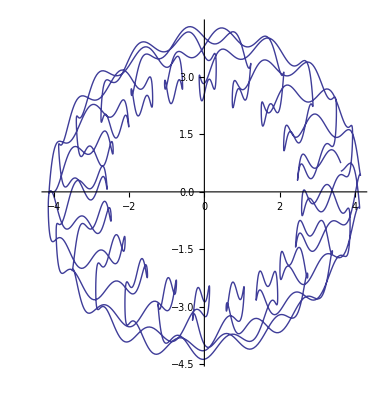

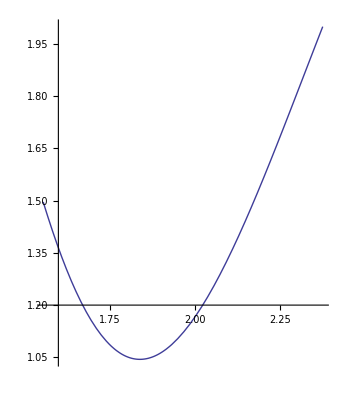

```mathematica
xp[x2_,y2_]:=3.375*Cos[2π*t]+x2*Cos[(2π+40 π/3)*t]-y2*Sin[(2π+40 π/3)*t]
yp [x2_,y2_]:=3.375*Sin[2π*t]+x2*Sin[(2π*40 π/3)*t]+y2*Cos[(2π+40 π/3)*t]
ParametricPlot[{xp[0,0],yp[0,0]},{t,0,3}]
ParametricPlot[{xp[.25,.75],yp[.25,.75]},{t,0,3}]
ParametricPlot[{xp[-1,2],yp[-1,2]},{t,0,.01}]
```